# Report Project II

Course code: IX1500
Date: 2018-10-04

Michel Ouadria, ouadria@kth.se
Rikard Jakobsson, rikjak@kth.se

Task 1: RSA cipher

## Summary

### Task

Professor Alice is sending a message to the student Bob according to the procedure in section Section.Subsection.4. You are supposed to crack the message. When translating to ASCII, you can assume the base 256.

```mathematica
nBob=126456119090476383371855906671054993650778797793018127;
eBob=7937;
```

```mathematica
cipher={60833078379832053733665235104517667174744887177103669,47845135110330425759238983903835414959478333031403660,29226436027122547212719862444995325439654173683124719,26852073219160460393476539289841435348076003235573562,18536789208272843521201394019815486297145984481554371,60946204295190537657611153931568067486237180585452998,23651682987715782801807742133012602969829495021520007,112630050746349041975951827486336529408641182025699787,46387928110260904731968713144311859620686048715174256,101614383351383083936620333816943396668613455381224570};
```

The numbers is the list seems to be of the same size. Why?

### Result

## Code

```mathematica
ClearAll["`*"]
nBob=126456119090476383371855906671054993650778797793018127;(*Public key*)
eBob=7937;(*Bobs public key*)
B = 256;(*Base for the ascii*)

FactorInteger[nBob]
pBob = 494991074232809803525292243;(*One of the two prime factors of n*)
qBob = 255471513878248459929909589;(*Second of the two...*)
phi = (pBob-1)*(qBob-1);(*Phi of any prime number is -1 since no prime number has no factor greater than one*)
GCD[phi,eBob];
dBob = PowerMod[eBob,-1,phi];

cAlice={60833078379832053733665235104517667174744887177103669,47845135110330425759238983903835414959478333031403660,29226436027122547212719862444995325439654173683124719,26852073219160460393476539289841435348076003235573562,18536789208272843521201394019815486297145984481554371,60946204295190537657611153931568067486237180585452998,23651682987715782801807742133012602969829495021520007,112630050746349041975951827486336529408641182025699787,46387928110260904731968713144311859620686048715174256,101614383351383083936620333816943396668613455381224570};

(*mFromAlice=PowerMod[cAlice[[1]],dBob,nBob];*)
readMessage[x_]:=(
mFromAlice=PowerMod[x,dBob,nBob];
q=mFromAlice;ascii={};
While[q≠0,
AppendTo[ascii,Mod[q,B]];
q=Quotient[q,B]
];
FromCharacterCode[ascii])
StringJoin[readMessage/@cAlice]
```

{{255471513878248459929909589,1},{494991074232809803525292243,1}}

Congratulations! You have now managed to crack the RSA cipher. This means that you have a pass grade for project 2. If you want to pursue a higher grade you need to solve one more problem.

Task 2: RSA decryption analysis

## Summary

### Task

Write a method RSAcrack[cipher,n,e] that will crack a standard RSA cipher and delivers clear text from the string cipher. When you are finished with your method, you should investigate how long it will take to crack the cipher of the English text “ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL.” for different sizes on your public key n (100-200 bits). Visualize your results in a proper graph. It is very important that you study the section 2.3 in the instructions. Your graph should lead you to a model where you can predict how long it would take to crack a cipher if n is 1024, 2048 bits or 4096 bits

Motivate your selected mathematical model!

### Result

### Discussion

### Conclusion

## Code

```mathematica
(*Bob wants to send a message to alice. He  pads it with m
Alice generates public and private key by generate a prime of same size, 100-200. 
Then, muliply to get n. 
Then to get Phi of n, (p-1)*(q-1)
Pick a small odd number that DOESN'T share a factor with Phi(N).
Finally, find d. 
*)
```

{}

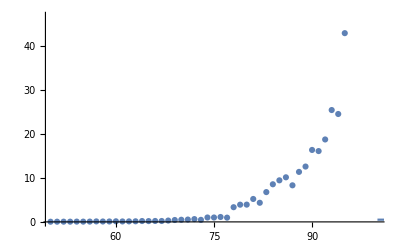

```mathematica
Remove["Global`*"];
B = 256;(*Base for the ascii*)
message = "ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL.";


GenerateKeys[num_] := (
randP =NextPrime[RandomInteger[{2^num,2^(num+1)-1}]];
randQ =NextPrime[RandomInteger[{2^num,2^(num+1)-1}]];
n = randP*randQ;
ϕ = (randP-1)*(randQ-1);

rndForE:=RandomInteger[{2^4,2^6+ 1}]; 

While[GCD[e=rndForE,ϕ]≠1];
(*$keys ={"keyN"->n,"keyE"->e};*)
keys = {e,n}

)
(*Test varaibles
nBob=126456119090476383371855906671054993650778797793018127;(*Public key*)
eBob=7937;(*Bobs public key*)
key =GenerateKeys[50];
eeBob = keys[[1]];
nnBob = keys[[2]];
"P value"
randP
"Q value"
randQ
"Bit length"
BitLength[nnBob]
(*/test variables*)*)


(*Crack the RSA*)
RSAcrack[cipher_,n_,e_]:=(
pq = FactorInteger[n];
     (*One of the two prime factors of n*)
p = pq[[1,1]];
q=pq[[2,1]];(*Second of the two...*)
phi = (p-1)*(q-1);(*Phi of any prime number is -1 since no prime number has no factor greater than one*)
GCD[phi,e];
d = PowerMod[e,-1,phi];
(*mFromAlice=PowerMod[cAlice[[1]],dBob,nBob];*)


readMessage[msg_]:=(
mFromAlice=PowerMod[msg,d,n];
qu=mFromAlice;
ascii={};
While[qu≠0,
AppendTo[ascii,Mod[qu,B]];
qu=Quotient[qu,B]
];
FromCharacterCode[ascii]);
StringJoin[readMessage/@cipher]
)

(*Splits the provided string into smaller string chunks of the provided size*)
chunk[string_,partSize_]:=(StringCases[string,RegularExpression[".{1,"<>ToString[partSize]<>"}"]]);
(*Gets char code from the provided string using the n and e keys*)
charCode[msg_,n_,e_]:=(mess =ToCharacterCode[msg]. B^(Range[StringLength[msg]]-1);
mOut= PowerMod[mess,e,n])
(*Creates a cipher using the public keys*)
RSAencrypt[msg_,n_,e_]:=(
cipher ={};
chunkat=chunk[msg,4];
(charCode[#,n,e])&/@chunkat)

testMsg ="ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL.";
(*test = RSAencrypt[testMsg,nnBob,eeBob];
RSAcrack[test,nnBob,eeBob]*)
listOfTiming = {};
testData = Range[50,100];

(*testTiming[time_]:=()*)
listOfTiming

(*For[i= 50,i<101,i++, GenerateKeys[i];ee = keys[[1]];nn=keys[[2]];crypt = RSAencrypt[message,nn,ee];AppendTo[listOfTiming,{i,Timing[RSAcrack[crypt,nn,ee]][[1]]}]]
listOfTiming*)



timelist={{{0.046891,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},50},{{0.049316,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},51},{{0.040534,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},52},{{0.056226,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},53},{{0.050325,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},54},{{0.073631,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},55},{{0.056282,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},56},{{0.082806,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},57},{{0.077497,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},58},{{0.0942,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},59},{{0.128801,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},60},{{0.148561,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},61},{{0.138184,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},62},{{0.202212,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},63},{{0.23488,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},64},{{0.242689,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},65},{{0.201249,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},66},{{0.152307,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},67},{{0.194841,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},68},{{0.288117,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},69},{{0.381733,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},70},{{0.353031,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},71},{{0.387156,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},72},{{0.464148,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},73},{{0.623461,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},74},{{0.984965,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},75},{{0.863751,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},76},{{0.78939,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},77},{{1.166248,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},78},{{3.801099,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},79},{{4.336117,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},80},{{3.607447,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},81},{{5.626473,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},82},{{3.963263,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},83},{{5.534229,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},84},{{7.178113,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},85},{{9.742031,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},86},{{8.832977,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},87},{{8.443968,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},88},{{12.099588,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},89},{{11.681414,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},90},{{17.863461,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},91},{{22.381151,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},92},{{10.368071,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},93},{{24.442973,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},94},{{49.249459,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},95},{{28.202286,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},96},{{53.349584,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},97},{{69.127599,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},98},{{107.959133,"ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL."},99}};

timeList ={{50,0.03978},{51,0.049216},{52,0.053028},{53,0.051833},{54,0.067854},{55,0.061266},{56,0.072162},{57,0.112672},{58,0.092},{59,0.098515},{60,0.135034},{61,0.104317},{62,0.120415},{63,0.136627},{64,0.196623},{65,0.182818},{66,0.20989},{67,0.204774},{68,0.30442},{69,0.430872},{70,0.487629},{71,0.532953},{72,0.637486},{73,0.465032},{74,1.001486},{75,0.999636},{76,1.114179},{77,0.966923},{78,3.338279},{79,3.911549},{80,3.924905},{81,5.207133},{82,4.345123},{83,6.770155},{84,8.547124},{85,9.443232},{86,10.13003},{87,8.31012},{88,11.359896},{89,12.573838},{90,16.345792},{91,16.090379},{92,18.726639},{93,25.41106},{94,24.511166},{95,42.877001},{96,55.379241},{97,50.707816},{98,68.04006},{99,104.666318},{100,107.593086}};

timePlot = ListPlot[timeList];
probabilityPlot =Plot[0.501219409637541,{x,100,200},PlotLabel->"0.501"];
Show[timePlot,probabilityPlot]
```

## Summary

### Discussion

### Conclusion

## Code